```mathematica
markers=Graphics`PlotMarkers[]
m1=markers[[All,1]];
m1[[2]]
```

{{●,10.96},{■,8.96},{◆,10.88},{▲,10.24},{▼,10.24},{○,10.24},{□,10.24},{◇,10.24},{△,11.136},{▽,11.136}}

■

```mathematica
Data = Import["C:\\Users\\Bayan Ali\\Desktop\\Wolframe_Languages_plots\\russian\\russian_updated_100.csv"];
x=Data[[All,1]];
y=Data[[All,2]] ;
da=Transpose[{x,y}];
```

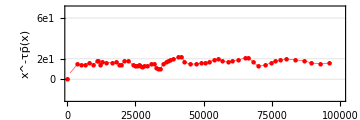

```mathematica
marker=Style[m1[[1]],FontSize->6];
f1=BSplineFunction[da];
s1=ParametricPlot[f1[t],{t,.0,53},
AxesOrigin->{.0,.0},
Mesh->All,
AspectRatio->1.5/4.5,
PlotStyle->{Red,Thickness[0.001]},
PlotRange->{{1100,1*10^5},{-2*10^1,7*10^1}},
GridLines -> {None,Automatic},
Frame->True,
FrameStyle->Directive[Thin,Black,Thickness[0.001]],
ImageSize-> Medium,Axes->False, FrameTicks->{{{{0,"0"},{2*10^1,"2e1"},{6*10^1,"6e1"}},None},{Automatic,None}}, FrameLabel->{Style[Row[{"x/",Subscript["x","c"]," (L)"}],FontFamily->"Times New Roman",10,Bold],Style[Row[{Superscript["x","-τ"],OverBar[" p"],"(x)"}],FontFamily->"Times New Roman",10,Bold]}
]/.
Point[x:{__Integer}]:>Map[Inset[marker,#]&,x]
```

```mathematica
Data90 = Import["C:\\Users\\Bayan Ali\\Desktop\\Wolframe_Languages_plots\\russian\\russian_updated_90.csv"];
```

```mathematica
x1=Data90[[All,1]];
y2=Data90[[All,2]] +d;
da1=Transpose[{x1,y2}];
```

```mathematica
d =2
```

2

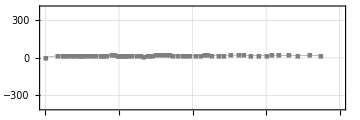

```mathematica
marker=Style[m1[[2]],FontSize->6];
f2=BSplineFunction[da1];
s2=ParametricPlot[f2[t],{t,.0, 53},
AxesOrigin->{.0,.0},
Mesh->All,
GridLines->Automatic ,
AspectRatio->1.5/4.5,
PlotStyle->{Gray,Thickness[0.001]},
PlotRange->{{0,1*10^5},{-4*10^2,4*10^2}},
GridLines -> {None,Automatic},
GridLinesStyle->Directive[Black,Dashed],
Frame->True,
FrameStyle->Directive[Thin,Black,Thickness[0.001]],
ImageSize-> Medium,Axes->False
]/.
Point[x:{__Integer}]:>Map[Inset[marker,#]&,x]
```

```mathematica
Length[Data90]
```

40636

```mathematica
Data80 = Import["C:\\Users\\Bayan Ali\\Desktop\\Wolframe_Languages_plots\\russian\\russian_updated_80.csv"];
Data70 = Import["C:\\Users\\Bayan Ali\\Desktop\\Wolframe_Languages_plots\\russian\\russian_updated_70.csv"];
Data60 = Import["C:\\Users\\Bayan Ali\\Desktop\\Wolframe_Languages_plots\\russian\\russian_updated_60.csv"];
Data50 = Import["C:\\Users\\Bayan Ali\\Desktop\\Wolframe_Languages_plots\\russian\\russian_updated_50.csv"];
```

```mathematica
da80=Transpose[{Data80[[All,1]],Data80[[All,2]] +2*d}];
da70 = Transpose[{Data70[[All,1]],Data70[[All,2]]+2.5*d}];
da60 = Transpose[{Data60[[All,1]],Data60[[All,2]]+3*d}];
da50 = Transpose[{Data50[[All,1]],Data50[[All,2]]+3.5*d}];
```

```mathematica
marker=Style[m1[[3]],FontSize->6];
f3=BSplineFunction[da80];
s3=ParametricPlot[f3[t],{t,.0,53},
AxesOrigin->{.0,.0},
GridLines->Automatic ,
Mesh->All,
AspectRatio->1.5/4.5,
PlotStyle->{Blue,Thickness[0.001]},
PlotRange->{{0,1*10^5},{-4*10^2,4*10^2}},
GridLines -> {None,Automatic},
GridLinesStyle->Directive[Black,Dashed],
Frame->True,
FrameStyle->Directive[Thin,Black,Thickness[0.001]],
ImageSize-> Medium,Axes->False
]/.
Point[x:{__Integer}]:>Map[Inset[marker,#]&,x];
marker=Style[m1[[4]],FontSize->6];
f4=BSplineFunction[da70];
s4=ParametricPlot[f4[t],{t,.0,53},
AxesOrigin->{.0,.0},
GridLines->Automatic ,
Mesh->All,
AspectRatio->1.5/4.5,
PlotStyle->{Yellow,Thickness[0.001]},
PlotRange->{{0,1*10^5},{-4*10^2,4*10^2}},
GridLines -> {None,Automatic},
GridLinesStyle->Directive[Black,Dashed],
Frame->True,
FrameStyle->Directive[Thin,Black,Thickness[0.001]],
ImageSize-> Medium,Axes->False
]/.
Point[x:{__Integer}]:>Map[Inset[marker,#]&,x];
marker=Style[m1[[5]],FontSize->6];
f5=BSplineFunction[da60];
s5=ParametricPlot[f5[t],{t,.0,53},
AxesOrigin->{.0,.0},
GridLines->Automatic ,
Mesh->All,
AspectRatio->1.5/4.5,
PlotStyle->{Orange,Thickness[0.001]},
PlotRange->{{0,1*10^5},{-4*10^2,4*10^2}},
GridLines -> {None,Automatic},
GridLinesStyle->Directive[Black,Dashed],
Frame->True,
FrameStyle->Directive[Thin,Black,Thickness[0.001]],
ImageSize-> Medium,Axes->False
]/.
Point[x:{__Integer}]:>Map[Inset[marker,#]&,x];
marker=Style[m1[[6]],FontSize->6];
f6=BSplineFunction[da50];
s6=ParametricPlot[f6[t],{t,.0,53},
AxesOrigin->{.0,.0},
GridLines->Automatic ,
Mesh->All,
AspectRatio->1.5/4.5,
PlotStyle->{Purple,Thickness[0.001]},
PlotRange->{{0,1*10^5},{-4*10^2,4*10^2}},
GridLines -> {None,Automatic},
GridLinesStyle->Directive[Black,Dashed],
Frame->True,
FrameStyle->Directive[Thin,Black,Thickness[0.001]],
ImageSize-> Medium,Axes->False
]/.
Point[x:{__Integer}]:>Map[Inset[marker,#]&,x];
```

```mathematica
res1=Show[s1,s2,s3,s4,s5,s6,PlotLabel->Style[HoldForm[Prussner-Russian],Bold],LabelStyle->{FontFamily->"Times New Roman",10,GrayLevel[0]},PlotMarkers->Automatic,ImageResolution->600];res11=Legended[res1,Placed[PointLegend[{Red,Gray,Blue,Yellow,Orange,Purple},{"L     ","0.9L","0.8L","0.7L","0.6L","0.5L"},LegendMarkers->Automatic,LegendMarkerSize->{8,8},LabelStyle->Directive[FontFamily->"Times New Roman",Black,8,Bold],LegendLayout->{"Row",2}],{{0.5,0},{0.5,1}}]]
```

-Graphics-

```mathematica
Export["C:\\Users\\Bayan Ali\\Desktop\\Wolframe_Languages_plots\\russian\\russian_Prussner.eps",res11,"EPS"]
Export["C:\\Users\\Bayan Ali\\Desktop\\Wolframe_Languages_plots\\russian\\russian_Prussner.png",res11,"PNG"]
Export["C:\\Users\\Bayan Ali\\Desktop\\Wolframe_Languages_plots\\russian\\russian_Prussner.svg",res11,"SVG"]
```

C:\Users\Bayan Ali\Desktop\Wolframe_Languages_plots\russian\russian_Prussner.eps

C:\Users\Bayan Ali\Desktop\Wolframe_Languages_plots\russian\russian_Prussner.png

C:\Users\Bayan Ali\Desktop\Wolframe_Languages_plots\russian\russian_Prussner.svg

```mathematica
"C:\\Users\\Bayan Ali\\Desktop\\Wolframe_Languages_plots\\russian\\russian_Prussner.eps"
```

```mathematica
"C:\\Users\\Bayan Ali\\Desktop\\Wolframe_Languages_plots\\russian\\russian_Prussner.png"
```

```mathematica
"C:\\Users\\Bayan Ali\\Desktop\\Wolframe_Languages_plots\\russian\\russian_Prussner.svg"
```

```mathematica
DataHill = Import["C:\\Users\\Bayan Ali\\Desktop\\Wolframe_Languages_plots\\russian\\russian_Hill_wolframe.csv"];
DataKs = Import["C:\\Users\\Bayan Ali\\Desktop\\Wolframe_Languages_plots\\russian\\russian_kolmogorov_wolframe.csv"];

daKs=Transpose[{DataKs[[All,1]],DataKs[[All,2]] }];
daksY = DataKs[[1,3]];
```

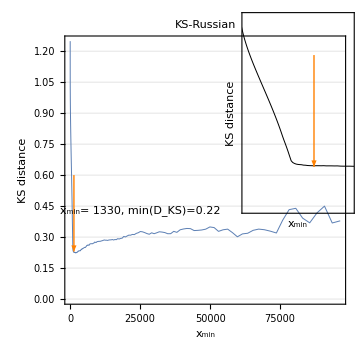

```mathematica
l1 = ListLinePlot[daKs,AxesOrigin->{0,0},
PlotRange->Full,
GridLines->{None,Automatic },
PlotStyle->{DarkBlue,Thickness[0.002]},
Frame->{{True,False},{True,False}},
FrameLabel->{{"KS distance",None},{Subscript["x","min"],None}},
ImageSize->Medium];
a={Arrowheads[Large],Arrow[{{1330,.6},{1330,0.23}}]};
l3 = Graphics[{Black,{Orange,a},Text[Style["x_min= 1330, min(D_KS)=0.22",FontFamily->"Times New Roman"],{25000,.43}]}];
res1 = Show[l1,l3,PlotLabel->HoldForm[KS - Russian],LabelStyle->{FontFamily->"Times New Roman",10,GrayLevel[0]}];
res3=Show[Graphics[{Rectangle[{0,0},{1,1},res1],Rectangle[{0.6,0.299},{1,1},res2]}]]
```

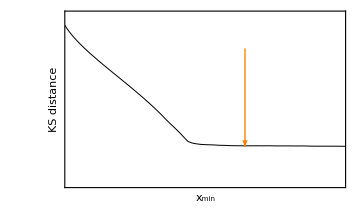

```mathematica
l4 = ListLinePlot[daKs,AxesOrigin->{0,0},
PlotRange->{{100,2000},{0,1.0}},
FrameTicks->None,
PlotStyle->{Black,Thickness[0.002]},
AxesLabel->{"x_min","KS distance"},
Frame->{{True,False},{True,False}},
FrameLabel->{{"KS distance",None},{Subscript["x","min"],None}},LabelStyle->{FontFamily->"Times New Roman",10},
ImageSize->Medium];
a={Arrowheads[Large],Arrow[{{1330,.8},{1330,0.22}}]};
l5 = Graphics[{Orange,a}];
res2 = Show[l4,l5]
```

```mathematica
Export["C:\\Users\\Bayan Ali\\Desktop\\Wolframe_Languages_plots\\russian\\russian_KS.eps",res3,"EPS"]
Export["C:\\Users\\Bayan Ali\\Desktop\\Wolframe_Languages_plots\\russian\\russian_KS.png",res3,"PNG"]
Export["C:\\Users\\Bayan Ali\\Desktop\\Wolframe_Languages_plots\\russian\\russian_KS.svg",res3,"SVG"]
```

C:\Users\Bayan Ali\Desktop\Wolframe_Languages_plots\russian\russian_KS.eps

C:\Users\Bayan Ali\Desktop\Wolframe_Languages_plots\russian\russian_KS.png

C:\Users\Bayan Ali\Desktop\Wolframe_Languages_plots\russian\russian_KS.svg